```mathematica
(* Convergence Tester: k sweep *)
(* Now, instead of computing single values and outputting a sequence for increasing m, 
we will do this repeateadly for increasing values of k, and then print a matrix. *)

(* ================ MACROS / USER PARAMETERS =================*)
(* f:= our function of m on S to be evaluated; 
k := offset for n. can be any integer so long as it doesn't bring n below 0.;
start:= first m to be checked in sequence. must be ≥ 1;
end:= last m to be checked in;
step := how much to increment by each iteration. determines what m are in our set S. 
e.g. step = 2 corresponds only even m.; *)
L=30;
terms = 10;
f3[m_] :=Floor[Sum[(2*(-1)^(n+1)*L*Sin[n*Pi*m/L])/(3*Pi*n),{n,1,terms}]];(*mark*)
f4[m_] :=Floor[Sum[(5*(-1)^(n+1)*L*Sin[n*Pi*m/L])/(6*Pi*n),{n,1,terms}]];(*mark*)
f5[m_] := Ceiling[(Sin[m]+m/2)];(*special case? converges to 2a(k) initially then diverges*)
f6[m_] := Ceiling[(Cos[m]+m/2)];(*special case? converges to 2a(k) initially then diverges*)
f55[m_] := Ceiling[(3*Sin[m/115]+m/2)];(*testing function*)



start=12; 
end=108;
step = 12; (* Don't change this. *)
kstart = 1;
kend = 15;
kstep = 1;

(* ====================================================== *)
```

```mathematica
(* Dependencies: *)
(* 
	Name: partitionN
 Mathematical Notation: N(r,m,n)
 Desc.: Gives the number of partitions of a positive integer, n, whose RANK is congruent to r, modulo m. 
*)

partitionN[r_,m_,n_]:=Module[{r0=r,m0=m,n0=n,counter=0,i,rank,list},
	list = IntegerPartitions[n0];
	Do[rank=Max[list[[i]]]-Length[list[[i]]]; 
	If[Mod[rank,m0]==Mod[r0,m0],counter++]; ,{i,Length[list]}];
counter]
```

```mathematica
(* Build our matrix *)

mList = {};
For[i=kstart, i ≤ kend, i+=kstep, (* For each value of k *)
seq = {};
For[j = start, j ≤ end, j+=step,   (* For each value in our sequence *)
AppendTo[seq, partitionN[f55[j],j,f55[j]+i]]
];
AppendTo[mList,seq];
];
```

```mathematica
MatrixForm[mList]
```

(2 | 2 | 2 | 3 | 3 | 3 | 5 | 5 | 5
1 | 1 | 1 | 2 | 2 | 2 | 4 | 4 | 4
3 | 3 | 3 | 5 | 5 | 5 | 8 | 8 | 8
3 | 3 | 3 | 5 | 5 | 5 | 9 | 9 | 9
6 | 6 | 6 | 9 | 9 | 9 | 14 | 14 | 14
6 | 6 | 6 | 10 | 10 | 10 | 16 | 16 | 16
11 | 11 | 11 | 16 | 16 | 16 | 25 | 25 | 25
11 | 12 | 12 | 18 | 18 | 18 | 28 | 28 | 28
18 | 19 | 19 | 28 | 28 | 28 | 41 | 41 | 41
21 | 22 | 22 | 32 | 32 | 32 | 49 | 49 | 49
32 | 33 | 33 | 46 | 46 | 46 | 67 | 67 | 67
34 | 38 | 38 | 55 | 55 | 55 | 80 | 80 | 80
52 | 55 | 55 | 76 | 76 | 76 | 109 | 109 | 109
59 | 64 | 65 | 90 | 90 | 90 | 129 | 129 | 129
82 | 88 | 89 | 122 | 122 | 122 | 171 | 171 | 171)

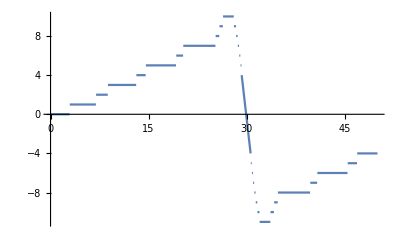

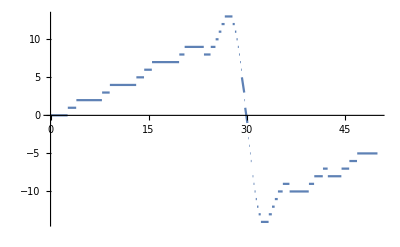

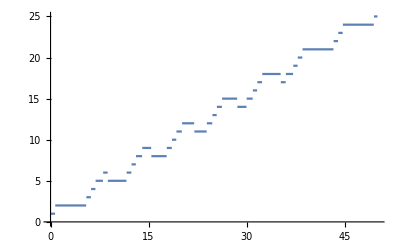

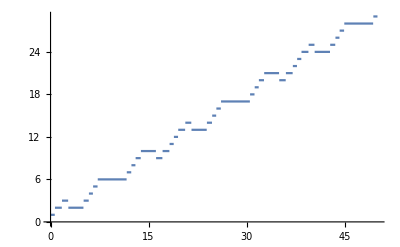

```mathematica
Plot[Floor[Sum[(2*(-1)^(n+1)*L*Sin[n*Pi*m/L])/(3*Pi*n),{n,1,terms}]], {m, 0, 50}]
Plot[Floor[Sum[(5*(-1)^(n+1)*L*Sin[n*Pi*m/L])/(6*Pi*n),{n,1,terms}]], {m, 0, 50}]
Plot[Ceiling[(Sin[m]+m/2)], {m, 0, 50}]
Plot[Ceiling[(Sin[m]+7*m/12)], {m, 0, 50}]
```

```mathematica
aList ={1,0,1,1,2,2,4,4,7,8,12,14,21,24,34};
twoAList={2,0,2,2,4,4,8,8,14,16,24,28,42,48,64};
bList={2,1,3,3,6,6,11,12,19,22,33,38,55,65,89};
cList={3,2,5,5,9,10,16,18,28,32,46,55,76,90,122};
dList={5,4,8,9,14,16,25,28,41,49,67,80,109,129,171};
testList=cList - aList
testList2= cList-bList
testList3=dList-cList
testList4=dList-aList
```

{2,2,4,4,7,8,12,14,21,24,34,41,55,66,88}

{1,1,2,2,3,4,5,6,9,10,13,17,21,25,33}

{2,2,3,4,5,6,9,10,13,17,21,25,33,39,49}

{4,4,7,8,12,14,21,24,34,41,55,66,88,105,137}